```mathematica
$Assumptions={d > 0, kx ∈ Reals, ky ∈ Reals, t ∈ Reals, t>0, qx ∈ Reals, qy ∈ Reals, θ ∈ Reals, ϵx ∈ Reals, ϵy ∈ Reals, ϵ ∈ Reals, ϵ > 0, tp >0, M > 0, ϕ ∈ Reals, t2 > 0, dkx ∈ Reals, dky ∈ Reals, qx ∈ Reals, qy ∈ Reals, q > 0}
```

{d>0,kx∈ℝ,ky∈ℝ,t∈ℝ,t>0,qx∈ℝ,qy∈ℝ,θ∈ℝ,ϵx∈ℝ,ϵy∈ℝ,ϵ∈ℝ,ϵ>0,tp>0,M>0,ϕ∈ℝ,t2>0,dkx∈ℝ,dky∈ℝ,qx∈ℝ,qy∈ℝ,q>0}

```mathematica
δ = {{0, d}, {-d Cos[30 Degree], - d Sin[30 Degree]}, {d Cos[30 Degree], - d Sin[30Degree]}}
```

{{0,d},{-(√3 d)/2,-d/2},{(√3 d)/2,-d/2}}

```mathematica
f[k_] := - t * Sum[Exp[-I  k . δ[[i]]], {i, 1, 3}]
```

```mathematica
H[k_] := {{0, -t Sum[Exp[I k.δ[[i]]], {i, 1, 3}]}, {-t Sum[Exp[-I k.δ[[i]]], {i, 1, 3}], 0}}
```

```mathematica
h[k_]:= -{ComplexExpand[Re[f[k]]], ComplexExpand[Im[f[k]]]}/t
```

```mathematica
K = {4 Pi/(3 Sqrt[3] d), 0}
```

{(4 π)/(3 √3 d),0}

```mathematica
FullSimplify[Expand[Norm[h[{kx, ky}]]] /. {d kx -> dkx, d ky -> dky}]
```

√(3+2 Cos[√3 dkx]+4 Cos[(√3 dkx)/2] Cos[(3 dky)/2])

```mathematica
Plot3D[{%7, -%7}, {dkx, -Pi, Pi}, {dky, -Pi, Pi}, PlotTheme->"Scientific", BoxRatios->Automatic, AxesLabel->{"d k_x", "d k_y", "E/t" }, Ticks->{{-Pi, 0, Pi}, {-Pi, 0, Pi}, Automatic}, PlotLegends->{"E_+", "E_-"}, ImageSize->Large, PlotPoints->100]
```

-Graphics3D-

```mathematica
FullSimplify[Series[f[K + {qx, qy}], {qx, 0, 1}, {qy, 0, 1}]] // Normal
```

3/2 ⅈ d qy t+qx ((3 d t)/2+3/4 ⅈ d^2 qy t)

```mathematica
linf[qx_, qy_] := 3/2 ⅈ d qy t+qx (3 d t)/2
```

```mathematica
FullSimplify[linf[qx, qy]]
```

3/2 d (qx+ⅈ qy) t

```mathematica
linH[qx_, qy_] := {{0, Conjugate[linf[qx, qy]]}, {linf[qx, qy], 0}}
```

```mathematica
FullSimplify[linH[qx, qy]] //MatrixForm
```

(0 | 3/2 d (qx-ⅈ qy) t
3/2 d (qx+ⅈ qy) t | 0)

```mathematica
Emp[qx_, qy_] := FullSimplify[Eigenvectors[linH[qx, qy]]*Sqrt[qx - I qy]]
```

```mathematica
FullSimplify[Emp[qx, qy]]
```

{{(-qx+ⅈ qy)/(√(qx+ⅈ qy)),√(qx-ⅈ qy)},{(qx-ⅈ qy)/(√(qx+ⅈ qy)),√(qx-ⅈ qy)}}

```mathematica
fp[k_] := - tp Exp[-I k.δ[[1]]] - t Sum[Exp[-I k.δ[[i]]], {i, 2, 3}]
```

```mathematica
hp[k_] := {ComplexExpand[Re[fp[k]]], ComplexExpand[Im[fp[k]]], 0}
```

```mathematica
FullSimplify[Expand[Norm[hp[{kx, ky}]]] /. {d kx -> dkx, d ky -> dky}]
```

√(2 t^2+tp^2+2 t^2 Cos[√3 dkx]+4 t tp Cos[(√3 dkx)/2] Cos[(3 dky)/2])

```mathematica
Manipulate[Plot3D[{%77 /. {t -> 1, tp-> α}, -%77 /. {t -> 1, tp->α}}, {dkx, -Pi, Pi}, {dky, -Pi, Pi}, PlotTheme->"Scientific", BoxRatios->Automatic, AxesLabel->{"d k_x", "d k_y", "E" }, Ticks->{{-Pi, 0, Pi}, {-Pi, 0, Pi}, Automatic}, PlotLegends->{"E_+", "E_-"}, ImageSize->Large, PlotPoints->25] , {α, 0.1, 3}]
```

```mathematica
M = {0, 2 Pi/(3 d)}
```

{0,(2 π)/(3 d)}

```mathematica
FullSimplify[fp[{kx, ky}] /. {tp -> 2 t}]
```

-2 ⅇ^(-ⅈ d ky) t (1+ⅇ^((3 ⅈ d ky)/2) Cos[1/2 √3 d kx])

```mathematica
fp2[{kx_, ky_}] := -2 ⅇ^(-ⅈ d ky) t (1+ⅇ^((3 ⅈ d ky)/2) Cos[1/2 √3 d kx])
```

```mathematica
FullSimplify[Series[fp2[M + {qx, qy}], {qx, 0, 1}, {qy, 0, 1}]] // Normal
```

-3 (-1)^(5/6) d qy t

```mathematica
linfp2[{qx_, qy_}] := -3 Exp[-I Pi/6] d qy t
```

```mathematica
linhp2[{qx_, qy_}] := {{0, Conjugate[linfp2[{qx, qy}]]}, {linfp2[{qx, qy}], 0}}
```

```mathematica
FullSimplify[linhp2[{qx, qy}]]
```

{{0,-3 (-1)^(1/6) d qy t},{3 (-1)^(5/6) d qy t,0}}

```mathematica
linfp2[{qx, qy}]
```

-3 d ⅇ^(-(ⅈ π)/6) qy t

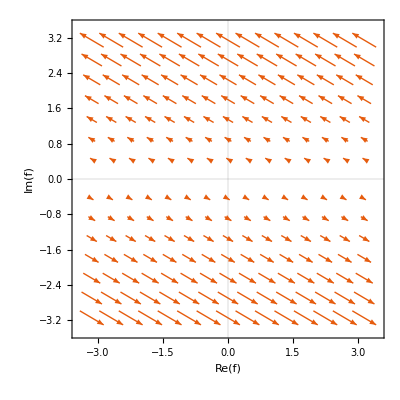

```mathematica
VectorPlot[{Re[linfp2[{qx, qy}]], Im[linfp2[{qx, qy}]]} /. {d -> 1, t-> 1}, {qx, -Pi, Pi}, {qy, -Pi, Pi}, FrameLabel->{"Re(f)", "Im(f)"}, Ticks->None, PlotTheme->"Scientific"]
```

```mathematica
Clear[M]
```

```mathematica
b = {δ[[1]] - δ[[2]], δ[[3]] - δ[[1]], δ[[2]] - δ[[3]]}
```

{{(√3 d)/2,(3 d)/2},{(√3 d)/2,-(3 d)/2},{-√3 d,0}}

```mathematica
d1[k_] := -h[k][[1]] t
d2[k_] := - h[k][[2]] t
d3[k_] := M - 2 t2 Sin[ϕ] Sum[Sin[k. b[[i]]], {i, 1, 3}]
```

```mathematica
dvec[k_] := {d1[k], d2[k], d3[k]}
```

```mathematica
ϵ0[k_] := 2 Cos[ϕ] Sum[Cos[k. b[[i]]], {i, 1, 3}]
```

```mathematica
H[k_] := ϵ0[k] PauliMatrix[0] + Sum[dvec[k][[i]] * PauliMatrix[i], {i, 1, 3}]
```

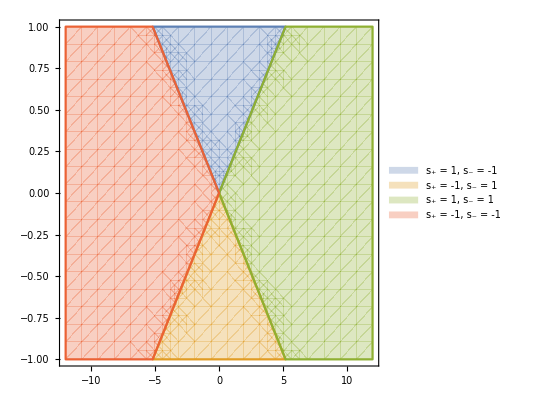

```mathematica
RegionPlot[{And[M - 3  Sqrt[3] s < 0, M + 3  Sqrt[3] s > 0], And[M - 3  Sqrt[3] s > 0, M + 3  Sqrt[3] s < 0],
And[M - 3  Sqrt[3] s > 0, M + 3  Sqrt[3] s > 0],
And[M - 3  Sqrt[3] s < 0, M + 3  Sqrt[3] s < 0]}, {M, - 6*2 , 6*2 }, {s, -1, 1} , PlotLegends->{" s_+ = 1, s_- = -1 ", " s_+ = -1, s_- = 1 ", " s_+ = 1, s_- = 1 ", " s_+ = -1, s_- = -1 "}]
```

```mathematica
FullSimplify[Series[ϵ0[K + {qx, qy}], {qx, 0, 1}, {qy, 0, 1}]] //Normal
```

-3 Cos[ϕ]

```mathematica
FullSimplify[Series[d1[K + {qx, qy}], {qx, 0, 1}, {qy, 0, 1}]] //Normal
```

(3 d qx t)/2

```mathematica
FullSimplify[Series[d2[K + {qx, qy}], {qx, 0, 1}, {qy, 0, 1}]] //Normal
```

(3 d qy t)/2+3/4 d^2 qx qy t

```mathematica
FullSimplify[Series[d3[K + {qx, qy}], {qx, 0, 1}, {qy, 0, 1}]] //Normal
```

M-3 √3 t2 Sin[ϕ]

```mathematica
FullSimplify[-3 Cos[ϕ]PauliMatrix[0] + (3 d qx t)/2 PauliMatrix[1] -3/2 d qy t PauliMatrix[2] + M+3 √3 t2 Sin[ϕ] PauliMatrix[3]]
```

{{M-3 Cos[ϕ]+3 √3 t2 Sin[ϕ],M+3/2 d (qx+ⅈ qy) t},{M+3/2 d (qx-ⅈ qy) t,M-3 Cos[ϕ]-3 √3 t2 Sin[ϕ]}}

```mathematica
FullSimplify[Series[f[K + {qx, qy}], {qx, 0, 1}, {qy, 0, 1}]] //Normal
```

3/2 ⅈ d qy t+qx ((3 d t)/2+3/4 ⅈ d^2 qy t)

```mathematica
f[{kx, ky}]
```

-(ⅇ^(ⅈ d ky)+ⅇ^(ⅈ (-1/2 √3 d kx-(d ky)/2))+ⅇ^(ⅈ (1/2 √3 d kx-(d ky)/2))) t